```mathematica
SetDirectory[NotebookDirectory[]];
tab=Import["efluxSImA1.mx"];
tab=Flatten[tab,1];
isexcluded[table_]:=Table[If[table[[i,3,1]]/1.>2.2 10^-12||table[[i,3,2]]/1.>8.8 10^-13||table[[i,3,3]]/1.>2.8 10^-13||table[[i,3,4]]/1.>8.1 10^-14||table[[i,3,5]]/1.>6.3 10^-14,1,0],{i,1,Length[tab]}]
exc=isexcluded[tab];
(*inttab=Table[{{tab⟦i,1⟧,tab⟦i,2⟧},If[exc[[i]]==1,1,0]},{i,1,Length[tab]}];
intfunc=Interpolation[inttab];*)
exctab={};
allowedtab={};
Do[If[exc[[i]]==1,exctab=Append[exctab,{tab⟦i,1⟧,tab⟦i,2⟧}]],{i,1,Length[tab]}]
Do[If[exc[[i]]==0,allowedtab=Append[allowedtab,{tab⟦i,1⟧,tab⟦i,2⟧}]],{i,1,Length[tab]}]
masses=DeleteDuplicates[Table[exctab[[i,1]],{i,1,Length[exctab]}]];
minexc={};
Do[
minexc=Append[minexc,particularmass=Select[exctab,#[[1]]==masses[[i]]&][[1]]],{i,1,Length[masses]}];
excfunc=Interpolation[minexc,InterpolationOrder->1];
ListLogLogPlot[{exctab,allowedtab,minexc},PlotRange-> All,Frame-> True,FrameStyle-> Black,LabelStyle-> 15,ImageSize->800, FrameLabel->{"DM mass (GeV)","σSI proton (cm^2)"},PlotStyle->{Red,Blue,Green},PlotMarkers-> {"■","■","■"}];
Show[%,LogLogPlot[excfunc[mdm],{mdm,Min[masses],Max[masses]}]]
```

-Graphics-

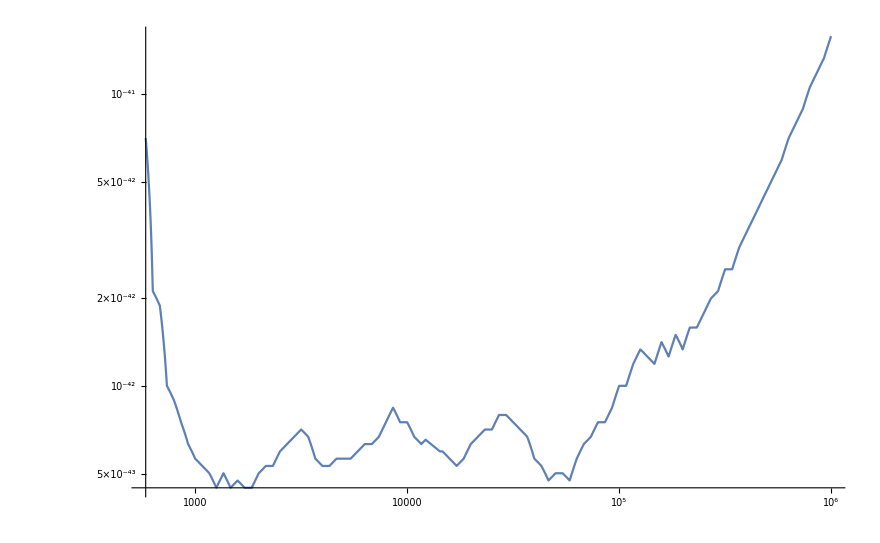

```mathematica
LogLogPlot[excfunc[mdm],{mdm,Min[masses],Max[masses]}]
```